```mathematica
"Map001Alg003Sec000001Nodes00000970Path010, freespace"
```

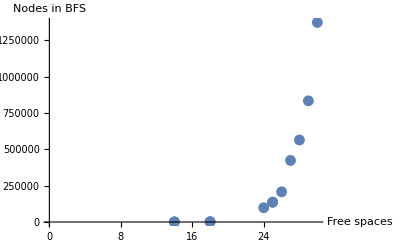

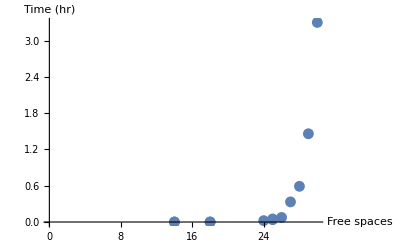

```mathematica
collecting = {
{1,3,1,970,10,14},
{1,4,0,970,10,14},
{2,3,1,2080,9,18},
{2,4,1,2080,9,18},
{3,3,181,136336,18,25},
{3,4,138,136336,18,25},
{5,4,82,98272,15,24},
{6,4,272,207641,16,26},
{7,4,1199,423440,17,27},
{8,4,2126,564237,17,28},
{9,4,5257,833483,18,29},
{10,4,11889,1372589,19,30}
};
ListPlot[Transpose[{collecting ⟦;;,6⟧,collecting ⟦;;,4⟧}],PlotRange->All,AxesLabel->{"Free spaces","Nodes in BFS"},AxesOrigin->{0,0},PlotRange->All]
ListPlot[Transpose[{collecting ⟦;;,6⟧,collecting ⟦;;,3⟧/60/60}],PlotRange->All,AxesLabel->{"Free spaces","Time (hr)"},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
collecting ⟦;;,4⟧
```

{970,970,2080,280,136336,136336}

```mathematica
N[ⅇ^24]/10^6
```

26489.1

### Compare number of moves between optimal and BFS

```mathematica
pairwise = {
{1,10,0,5,10},
{2,10,0,5,14},
{3,10,0,5,39},
{4,10,0,5,36},
{5,10,0,5,26},
{6,10,0,5,27},
{7,10,0,5,30},
{8,10,0,5,30},
{9,10,0,5,34},
{10,10,0,5,36},
{11,10,0,5,40},
{12,10,0,5,41}
};
```

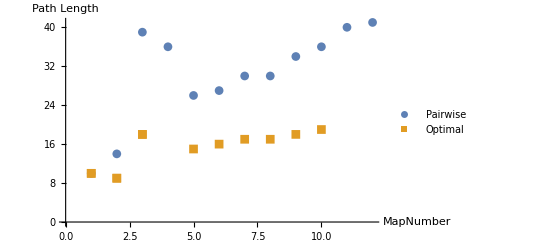

```mathematica
ListPlot[{
Transpose[{pairwise ⟦;;,1⟧,pairwise ⟦;;,5⟧}],
Transpose[{collecting ⟦;;,1⟧,collecting ⟦;;,5⟧}]
},PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"MapNumber","Path Length"},AxesOrigin->{0,0},PlotRange->All,PlotLegends->{"Pairwise","Optimal"}]
```

```mathematica
N[11889/60/60]
```

3.3025